```mathematica
Clear[k,k1,k2,k3,k4,k5, k6, k7, k8, k9, kdu,kdv];
HighestSpaceDerivative[eqn_]:=Module[{orders=Cases[eqn,Derivative[orders__]->{orders},Infinity,Heads->True],spaceOrders},spaceOrders=Table[ord[[1]],{ord,orders}];
Max[spaceOrders]];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["NDSolve`FEM`"]
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Mathematical Description
```

Description Mathematical

Let’s define the system of equations under study:

{(∂ARR1(x,t))/(∂t)=f(aux, PLT, ARR1)+D_ARR1·∇^2 ARR1(x,t)
(∂PLT(x,t))/(∂t)=g(aux, PLT, ARR1)+D_PLT·∇^2 PLT(x,t)
(∂aux(x,t))/(∂t)=h(aux, PLT, ARR1)+D_aux·∇^2 aux(x,t)      (1)

ARR1= ARR1; PLT = PLT; aux = aux

{(∂ARR1(x,t))/(∂t)= f(aux, PLT, ARR1)                                                                  
(∂PLT(x,t))/(∂t)= g(aux, PLT, ARR1)  +  D_PLT·∇^2 PLT(x,t)                        
(∂aux(x,t))/(∂t)=h(aux, PLT, ARR1)+D_aux·∇^2 aux(x,t)+P_PIN·∇aux(x,t)

## The system represents reaction-diffusion PDEs for auxin, PLT and ARR1

## f,g,h represent the local reactions (for each component); D_ARR1, D_PLT, D_aux represent diffusion coefficients of each component

## We want to find the steady state of the system , which is given by:

f(OverBar[ARR1],OverBar[PLT],OverBar[aux])=g(OverBar[ARR1],OverBar[PLT],OverBar[aux])=h(OverBar[ARR1],OverBar[PLT],OverBar[aux])=0

## We can rewrite the system in a matrix form:

(ARR1
PLT
aux)_t=γ(f'(aux, PLT, ARR1)
g'(aux, PLT, ARR1)
h'(aux, PLT, ARR1))+(D_ARR1·ARR1_xx
D_PLT·PLT_xx
D_aux·aux_xx);

Now we define the reaction terms for each equation:

```mathematica
f[ARR1,PLT,aux]:=k1 *ARR1 + k2 *PLT+k3* aux  +alpha;(*ARR1*)
g[ARR1,PLT,aux]:=k4  *ARR1 + k5 *PLT + k6 * aux + beta;(*Plethoras*)
h[ARR1,PLT,aux]:=k7 *ARR1 +k8 *PLT + k9  * aux +gamma;
equilibriumPoint=Solve[{f[ARR1,PLT,aux]==0,g[ARR1,PLT,aux]==0,h[ARR1,PLT,aux]==0},{ARR1,PLT,aux}][[1]]
```

{ARR1→-((gamma k3 k5-gamma k2 k6-beta k3 k8+alpha k6 k8+beta k2 k9-alpha k5 k9)/(k3 k5 k7-k2 k6 k7-k3 k4 k8+k1 k6 k8+k2 k4 k9-k1 k5 k9)),PLT→-((-gamma k3 k4+gamma k1 k6+beta k3 k7-alpha k6 k7-beta k1 k9+alpha k4 k9)/(k3 k5 k7-k2 k6 k7-k3 k4 k8+k1 k6 k8+k2 k4 k9-k1 k5 k9)),aux→-((-gamma k2 k4+gamma k1 k5+beta k2 k7-alpha k5 k7-beta k1 k8+alpha k4 k8)/(-k3 k5 k7+k2 k6 k7+k3 k4 k8-k1 k6 k8-k2 k4 k9+k1 k5 k9))}

```mathematica
ourParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1};
```

```mathematica
f1[ARR1,PLT,aux]:=k1 *ARR1 + k2 *PLT+k3* aux  +alpha;(*ARR1*)
g1[ARR1,PLT,aux]:=k4  *ARR1 + k5 *PLT + k6 * aux + beta;(*Plethoras*)
h1[ARR1,PLT,aux]:=k7 *ARR1 +k8 *PLT + k9  * aux +gamma;
equilibriumPoint1=Solve[{f[ARR1,PLT,aux]==0,g[ARR1,PLT,aux]==0,h[ARR1,PLT,aux]==0},{alpha,beta,gamma}][[1]]/.ourParams
```

{alpha→-aux+1.98 PLT,beta→0.48 ARR1,gamma→ARR1+0.1 aux-0.2 PLT}

```mathematica
equilibriumPoint1/.ARR1->0.8/.aux->1/.PLT->1
```

{alpha→0.98,beta→0.384,gamma→0.7}

## The linearized form is: w_t=γJw+DΔw, where J is the Jacobian matrix, defined as:

J=(f_ARR1 | f_PLT | f_aux
g_ARR1 | g_PLT | g_aux
h_ARR1 | h_PLT | h_aux)=(f_ARR1 | f_PLT | f_aux
g_ARR1 | g_PLT | g_aux
h_ARR1 | h_PLT | h_aux)

and D is the diffusion matrix:

```mathematica
J=({{Subscript[f, ARR1], Subscript[f, PLT], Subscript[f, aux]}, {Subscript[g, ARR1], Subscript[g, PLT], Subscript[g, aux]}, {Subscript[h, ARR1], Subscript[h, PLT], Subscript[h, aux]}})
```

{{f_ARR1,f_PLT,f_aux},{g_ARR1,g_PLT,g_aux},{h_ARR1,h_PLT,h_aux}}

```mathematica
{{Subscript[f, ARR1],Subscript[f, PLT],Subscript[f, aux]},{Subscript[g, ARR1],Subscript[g, PLT],Subscript[g, aux]},{Subscript[h, ARR1],Subscript[h, PLT],Subscript[h, aux]}}
```

{{f_ARR1,f_PLT,f_aux},{g_ARR1,g_PLT,g_aux},{h_ARR1,h_PLT,h_aux}}

## The characteristic polynomial of the linearized system is defined as:

Det[λI-γJ+Dk^2]=0,

I is the identiy matrix:

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

k is the wavenumber.

## In the absence of diffusion (the matrix D=0), the fixed point is stable if the eingenvalues of γJ have negative real part. The eigenvalues are given by the characteristic equation:

## λ^2-γtr(J)λ+γ^2det(J)=0

## Re(λ_(1,2))<0 for the homogeous system if and only if:

tr(J)<0 →f_ARR1+g_PLT+h_aux

det(J)>0→f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT>0

```mathematica
Det[J]
```

f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT

```mathematica
Subscript[f, PLT] Subscript[g, aux] Subscript[h, ARR1]-Subscript[f, aux] Subscript[g, PLT] Subscript[h, ARR1]-Subscript[f, PLT] Subscript[g, ARR1] Subscript[h, aux]+Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux]+Subscript[f, aux] Subscript[g, ARR1] Subscript[h, PLT]-Subscript[f, ARR1] Subscript[g, aux] Subscript[h, PLT]
```

f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT

```mathematica
Tr[J]
```

f_ARR1+g_PLT+h_aux

```mathematica
Subscript[f, ARR1]+Subscript[g, PLT]+Subscript[h, aux]
```

f_ARR1+g_PLT+h_aux

```mathematica
charpol= λ^2-γ*Tr[J]*λ+γ^2 Det[J]
```

λ^2-γ λ (f_ARR1+g_PLT+h_aux)+γ^2 (f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT)

```mathematica
λ^2-γ λ (Subscript[f, ARR1]+Subscript[g, PLT]+Subscript[h, aux])+γ^2 (Subscript[f, PLT] Subscript[g, aux] Subscript[h, ARR1]-Subscript[f, aux] Subscript[g, PLT] Subscript[h, ARR1]-Subscript[f, PLT] Subscript[g, ARR1] Subscript[h, aux]+Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux]+Subscript[f, aux] Subscript[g, ARR1] Subscript[h, PLT]-Subscript[f, ARR1] Subscript[g, aux] Subscript[h, PLT])
```

λ^2-γ λ (f_ARR1+g_PLT+h_aux)+γ^2 (f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT)

```mathematica
λ^2-(k1+k5+k9) λ (Piecewise[{{(2.*^-6)/(1+ⅇ^(-0.025 x) t), 0<x<200||x==0||x==200}, {1.*^-7, True}}])+(-k3 k5 k7+k2 k6 k7+k3 k4 k8-k1 k6 k8-k2 k4 k9+k1 k5 k9) (Piecewise[{{(2.*^-6)/(1+ⅇ^(-0.025 x) t), 0<x<200||x==0||x==200}, {1.*^-7, True}}])^2
```

λ^2-(k1+k5+k9) λ (Piecewise[{{(2.×10^-6)/(1+ⅇ^(-0.025 x) t), 0<x<200||x==0||x==200}, {1.×10^-7, True}}])+(-k3 k5 k7+k2 k6 k7+k3 k4 k8-k1 k6 k8-k2 k4 k9+k1 k5 k9) (Piecewise[{{(2.×10^-6)/(1+ⅇ^(-0.025 x) t), 0<x<200||x==0||x==200}, {1.×10^-7, True}}])^2

```mathematica
Solve[charpol==0,λ]
```

{{λ→1/2 (γ f_ARR1+γ g_PLT+γ h_aux-γ √(f_ARR1^2+2 f_ARR1 g_PLT+g_PLT^2-4 f_PLT g_aux h_ARR1+4 f_aux g_PLT h_ARR1+2 f_ARR1 h_aux+4 f_PLT g_ARR1 h_aux+2 g_PLT h_aux-4 f_ARR1 g_PLT h_aux+h_aux^2-4 f_aux g_ARR1 h_PLT+4 f_ARR1 g_aux h_PLT))},{λ→1/2 (γ f_ARR1+γ g_PLT+γ h_aux+γ √(f_ARR1^2+2 f_ARR1 g_PLT+g_PLT^2-4 f_PLT g_aux h_ARR1+4 f_aux g_PLT h_ARR1+2 f_ARR1 h_aux+4 f_PLT g_ARR1 h_aux+2 g_PLT h_aux-4 f_ARR1 g_PLT h_aux+h_aux^2-4 f_aux g_ARR1 h_PLT+4 f_ARR1 g_aux h_PLT))}}

## In presence of diffusion, the fixed point will become unstable. Let us define diffusion matrix as:

```mathematica
Diff=({{Subscript[D, ARR1], 0, 0}, {0, Subscript[D, PLT], 0}, {0, 0, Subscript[D, aux]}})
```

{{D_ARR1,0,0},{0,D_PLT,0},{0,0,D_aux}}

Recalling the full char. polynomium Det[λI-γJ+Dk^2]=0:

```mathematica
(*M=({{λ-γ*Subscript[f, ARR1]+k^2*Subscript[D, ARR1], -γ*Subscript[f, PLT], -γ*Subscript[f, aux]}, {-γ*Subscript[g, ARR1], λ-γ*Subscript[g, PLT]+k^2*Subscript[D, PLT], -γ*Subscript[g, aux]}, {-γ*Subscript[h, ARR1], -γ*Subscript[h, PLT], λ-γ*Subscript[h, aux]+k^2 Subscript[D, aux]}});*)
```

```mathematica
my=({{-Subscript[f, ARR1], -Subscript[f, PLT], -Subscript[f, aux]}, {-Subscript[g, ARR1], -Subscript[g, PLT]+k^2*Subscript[D, PLT], -Subscript[g, aux]}, {-Subscript[h, ARR1], -Subscript[h, PLT], -Subscript[h, aux]+k^2 Subscript[D, aux]}})
```

{{-f_ARR1,-f_PLT,-f_aux},{-g_ARR1,k^2 D_PLT-g_PLT,-g_aux},{-h_ARR1,-h_PLT,-k^2 D_aux h_aux}}

```mathematica
lambda1=Solve[CharacteristicPolynomial[my,λ]==0,λ][[1]]
```

{λ→1/3 (k^2 D_PLT-f_ARR1-g_PLT-k^2 D_aux h_aux)+(2^(1/3) (-(k^2 D_PLT-f_ARR1-g_PLT-k^2 D_aux h_aux)^2-3 (k^2 D_PLT f_ARR1+f_PLT g_ARR1-f_ARR1 g_PLT+f_aux h_ARR1+k^4 D_aux D_PLT h_aux-k^2 D_aux f_ARR1 h_aux-k^2 D_aux g_PLT h_aux+g_aux h_PLT)))/(3 (-2 k^6 D_PLT^3-3 k^4 D_PLT^2 f_ARR1+3 k^2 D_PLT f_ARR1^2+2 f_ARR1^3-9 k^2 D_PLT f_PLT g_ARR1+9 f_ARR1 f_PLT g_ARR1+6 k^4 D_PLT^2 g_PLT+6 k^2 D_PLT f_ARR1 g_PLT-3 f_ARR1^2 g_PLT+9 f_PLT g_ARR1 g_PLT-6 k^2 D_PLT g_PLT^2-3 f_ARR1 g_PLT^2+2 g_PLT^3+18 k^2 D_PLT f_aux h_ARR1+9 f_ARR1 f_aux h_ARR1+27 f_PLT g_aux h_ARR1-18 f_aux g_PLT h_ARR1-3 k^6 D_aux D_PLT^2 h_aux-12 k^4 D_aux D_PLT f_ARR1 h_aux-3 k^2 D_aux f_ARR1^2 h_aux-18 k^2 D_aux f_PLT g_ARR1 h_aux+6 k^4 D_aux D_PLT g_PLT h_aux+12 k^2 D_aux f_ARR1 g_PLT h_aux-3 k^2 D_aux g_PLT^2 h_aux+9 k^2 D_aux f_aux h_ARR1 h_aux+3 k^6 D_aux^2 D_PLT h_aux^2-3 k^4 D_aux^2 f_ARR1 h_aux^2-3 k^4 D_aux^2 g_PLT h_aux^2+2 k^6 D_aux^3 h_aux^3+27 f_aux g_ARR1 h_PLT-9 k^2 D_PLT g_aux h_PLT-18 f_ARR1 g_aux h_PLT+9 g_aux g_PLT h_PLT+9 k^2 D_aux g_aux h_aux h_PLT+√((-2 k^6 D_PLT^3-3 k^4 D_PLT^2 f_ARR1+3 k^2 D_PLT f_ARR1^2+2 f_ARR1^3-9 k^2 D_PLT f_PLT g_ARR1+9 f_ARR1 f_PLT g_ARR1+6 k^4 D_PLT^2 g_PLT+6 k^2 D_PLT f_ARR1 g_PLT-3 f_ARR1^2 g_PLT+9 f_PLT g_ARR1 g_PLT-6 k^2 D_PLT g_PLT^2-3 f_ARR1 g_PLT^2+2 g_PLT^3+18 k^2 D_PLT f_aux h_ARR1+9 f_ARR1 f_aux h_ARR1+27 f_PLT g_aux h_ARR1-18 f_aux g_PLT h_ARR1-3 k^6 D_aux D_PLT^2 h_aux-12 k^4 D_aux D_PLT f_ARR1 h_aux-3 k^2 D_aux f_ARR1^2 h_aux-18 k^2 D_aux f_PLT g_ARR1 h_aux+6 k^4 D_aux D_PLT g_PLT h_aux+12 k^2 D_aux f_ARR1 g_PLT h_aux-3 k^2 D_aux g_PLT^2 h_aux+9 k^2 D_aux f_aux h_ARR1 h_aux+3 k^6 D_aux^2 D_PLT h_aux^2-3 k^4 D_aux^2 f_ARR1 h_aux^2-3 k^4 D_aux^2 g_PLT h_aux^2+2 k^6 D_aux^3 h_aux^3+27 f_aux g_ARR1 h_PLT-9 k^2 D_PLT g_aux h_PLT-18 f_ARR1 g_aux h_PLT+9 g_aux g_PLT h_PLT+9 k^2 D_aux g_aux h_aux h_PLT)^2+4 (-(k^2 D_PLT-f_ARR1-g_PLT-k^2 D_aux h_aux)^2-3 (k^2 D_PLT f_ARR1+f_PLT g_ARR1-f_ARR1 g_PLT+f_aux h_ARR1+k^4 D_aux D_PLT h_aux-k^2 D_aux f_ARR1 h_aux-k^2 D_aux g_PLT h_aux+g_aux h_PLT))^3))^(1/3))-1/(3 2^(1/3))(-2 k^6 D_PLT^3-3 k^4 D_PLT^2 f_ARR1+3 k^2 D_PLT f_ARR1^2+2 f_ARR1^3-9 k^2 D_PLT f_PLT g_ARR1+9 f_ARR1 f_PLT g_ARR1+6 k^4 D_PLT^2 g_PLT+6 k^2 D_PLT f_ARR1 g_PLT-3 f_ARR1^2 g_PLT+9 f_PLT g_ARR1 g_PLT-6 k^2 D_PLT g_PLT^2-3 f_ARR1 g_PLT^2+2 g_PLT^3+18 k^2 D_PLT f_aux h_ARR1+9 f_ARR1 f_aux h_ARR1+27 f_PLT g_aux h_ARR1-18 f_aux g_PLT h_ARR1-3 k^6 D_aux D_PLT^2 h_aux-12 k^4 D_aux D_PLT f_ARR1 h_aux-3 k^2 D_aux f_ARR1^2 h_aux-18 k^2 D_aux f_PLT g_ARR1 h_aux+6 k^4 D_aux D_PLT g_PLT h_aux+12 k^2 D_aux f_ARR1 g_PLT h_aux-3 k^2 D_aux g_PLT^2 h_aux+9 k^2 D_aux f_aux h_ARR1 h_aux+3 k^6 D_aux^2 D_PLT h_aux^2-3 k^4 D_aux^2 f_ARR1 h_aux^2-3 k^4 D_aux^2 g_PLT h_aux^2+2 k^6 D_aux^3 h_aux^3+27 f_aux g_ARR1 h_PLT-9 k^2 D_PLT g_aux h_PLT-18 f_ARR1 g_aux h_PLT+9 g_aux g_PLT h_PLT+9 k^2 D_aux g_aux h_aux h_PLT+√((-2 k^6 D_PLT^3-3 k^4 D_PLT^2 f_ARR1+3 k^2 D_PLT f_ARR1^2+2 f_ARR1^3-9 k^2 D_PLT f_PLT g_ARR1+9 f_ARR1 f_PLT g_ARR1+6 k^4 D_PLT^2 g_PLT+6 k^2 D_PLT f_ARR1 g_PLT-3 f_ARR1^2 g_PLT+9 f_PLT g_ARR1 g_PLT-6 k^2 D_PLT g_PLT^2-3 f_ARR1 g_PLT^2+2 g_PLT^3+18 k^2 D_PLT f_aux h_ARR1+9 f_ARR1 f_aux h_ARR1+27 f_PLT g_aux h_ARR1-18 f_aux g_PLT h_ARR1-3 k^6 D_aux D_PLT^2 h_aux-12 k^4 D_aux D_PLT f_ARR1 h_aux-3 k^2 D_aux f_ARR1^2 h_aux-18 k^2 D_aux f_PLT g_ARR1 h_aux+6 k^4 D_aux D_PLT g_PLT h_aux+12 k^2 D_aux f_ARR1 g_PLT h_aux-3 k^2 D_aux g_PLT^2 h_aux+9 k^2 D_aux f_aux h_ARR1 h_aux+3 k^6 D_aux^2 D_PLT h_aux^2-3 k^4 D_aux^2 f_ARR1 h_aux^2-3 k^4 D_aux^2 g_PLT h_aux^2+2 k^6 D_aux^3 h_aux^3+27 f_aux g_ARR1 h_PLT-9 k^2 D_PLT g_aux h_PLT-18 f_ARR1 g_aux h_PLT+9 g_aux g_PLT h_PLT+9 k^2 D_aux g_aux h_aux h_PLT)^2+4 (-(k^2 D_PLT-f_ARR1-g_PLT-k^2 D_aux h_aux)^2-3 (k^2 D_PLT f_ARR1+f_PLT g_ARR1-f_ARR1 g_PLT+f_aux h_ARR1+k^4 D_aux D_PLT h_aux-k^2 D_aux f_ARR1 h_aux-k^2 D_aux g_PLT h_aux+g_aux h_PLT))^3))^(1/3)}

```mathematica
Det[M]==0;
```

The char polynomium (dispersion relation) is (from Rapovich  2014):

```mathematica
CharacteristicPolynomial[my,λ]
```

-(-λ f_aux+k^2 D_PLT f_aux+f_PLT g_aux-f_aux g_PLT) h_ARR1+(λ^2-k^2 λ D_PLT+λ f_ARR1-k^2 D_PLT f_ARR1-f_PLT g_ARR1+λ g_PLT+f_ARR1 g_PLT) (-λ-k^2 D_aux h_aux)+(-f_aux g_ARR1+λ g_aux+f_ARR1 g_aux) h_PLT

```mathematica
Eigenvalues[my]
```

{Root[#1^3+k^2 D_PLT f_aux h_ARR1+f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-k^4 D_aux D_PLT f_ARR1 h_aux-k^2 D_aux f_PLT g_ARR1 h_aux+k^2 D_aux f_ARR1 g_PLT h_aux+#1^2 (-k^2 D_PLT+f_ARR1+g_PLT+k^2 D_aux h_aux)+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+#1 (-k^2 D_PLT f_ARR1-f_PLT g_ARR1+f_ARR1 g_PLT-f_aux h_ARR1-k^4 D_aux D_PLT h_aux+k^2 D_aux f_ARR1 h_aux+k^2 D_aux g_PLT h_aux-g_aux h_PLT)&,1],Root[#1^3+k^2 D_PLT f_aux h_ARR1+f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-k^4 D_aux D_PLT f_ARR1 h_aux-k^2 D_aux f_PLT g_ARR1 h_aux+k^2 D_aux f_ARR1 g_PLT h_aux+#1^2 (-k^2 D_PLT+f_ARR1+g_PLT+k^2 D_aux h_aux)+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+#1 (-k^2 D_PLT f_ARR1-f_PLT g_ARR1+f_ARR1 g_PLT-f_aux h_ARR1-k^4 D_aux D_PLT h_aux+k^2 D_aux f_ARR1 h_aux+k^2 D_aux g_PLT h_aux-g_aux h_PLT)&,2],Root[#1^3+k^2 D_PLT f_aux h_ARR1+f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-k^4 D_aux D_PLT f_ARR1 h_aux-k^2 D_aux f_PLT g_ARR1 h_aux+k^2 D_aux f_ARR1 g_PLT h_aux+#1^2 (-k^2 D_PLT+f_ARR1+g_PLT+k^2 D_aux h_aux)+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+#1 (-k^2 D_PLT f_ARR1-f_PLT g_ARR1+f_ARR1 g_PLT-f_aux h_ARR1-k^4 D_aux D_PLT h_aux+k^2 D_aux f_ARR1 h_aux+k^2 D_aux g_PLT h_aux-g_aux h_PLT)&,3]}

```mathematica
charpolfull=λ^3+Subscript[a, 1] λ^2+Subscript[a, 2] λ+Subscript[a, 3]
```

λ^3+λ^2 a_1+λ a_2+a_3

```mathematica
Collect[charpolfull,k]
```

λ^3+λ^2 a_1+λ a_2+a_3

```mathematica
Clear[k1,k2,k3,k4,k5,k6,k7,k8,k9]
```

```mathematica
charpolsol=Solve[charpolfull==0,λ];

Tr[M]/.γ-> 1/.λ-> 0

Subscript[a, 1]:=−Subscript[f, ARR1]−Subscript[h, aux]−Subscript[g, PLT]+(Subscript[D, ARR1]+Subscript[D, PLT]+Subscript[D, aux])k^2
Subscript[a, 2]:=Subscript[f, ARR1] Subscript[h, aux]+Subscript[f, ARR1] Subscript[g, PLT]+Subscript[g, PLT] Subscript[h, aux]−Subscript[h, PLT] Subscript[g, aux]−Subscript[f, PLT] Subscript[g, ARR1]−Subscript[f, aux] Subscript[h, ARR1]−k^2(Subscript[D, aux] Subscript[g, PLT]+Subscript[D, PLT] Subscript[h, aux]+Subscript[D, ARR1] Subscript[h, aux]+Subscript[D, ARR1] Subscript[g, PLT]+Subscript[D, PLT] Subscript[f, ARR1]+Subscript[D, aux] Subscript[f, ARR1])+k^4(Subscript[D, PLT] Subscript[D, aux]+Subscript[D, PLT] Subscript[D, ARR1]+Subscript[D, ARR1] Subscript[D, aux])(*Subscript[a, 3]:= -Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux]+Subscript[f, ARR1] Subscript[h, PLT] Subscript[g, aux]+Subscript[g, ARR1] Subscript[f, PLT] Subscript[h, aux]-Subscript[h, ARR1] Subscript[f, PLT] Subscript[g, aux]-Subscript[g, ARR1] Subscript[h, PLT] Subscript[f, aux]+Subscript[h, ARR1] Subscript[g, PLT] Subscript[f, aux] + k^2 (Subscript[D, aux] Subscript[g, ARR1] Subscript[f, PLT]-Subscript[D, PLT] Subscript[h, ARR1] Subscript[f, aux] -Subscript[D, ARR1] Subscript[h, PLT] Subscript[g, aux] +Subscript[D, ARR1] Subscript[g, PLT] Subscript[h, aux] +Subscript[D, PLT] Subscript[f, ARR1] Subscript[h, aux] +Subscript[D, aux] Subscript[g, PLT] Subscript[f, ARR1])-k^4 (Subscript[D, PLT] Subscript[D, ARR1] Subscript[h, aux]+Subscript[D, ARR1] Subscript[D, aux] Subscript[g, PLT]+Subscript[D, PLT] Subscript[D, aux] Subscript[f, ARR1])+k^6 Subscript[D, PLT] Subscript[D, ARR1] Subscript[D, aux];*)
Subscript[a, 3]:=- Subscript[D, PLT]  Subscript[D, aux] Subscript[f, ARR1] k^4+ k^2 (Subscript[D, PLT] (Subscript[h, aux] Subscript[f, ARR1] - Subscript[h, ARR1] Subscript[f, aux]) + Subscript[D, aux] (Subscript[g, PLT] Subscript[f, ARR1] - Subscript[f, PLT] Subscript[g, ARR1]))-Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux]+Subscript[f, ARR1] Subscript[h, PLT] Subscript[g, aux]+Subscript[g, ARR1] Subscript[f, PLT] Subscript[h, aux]-Subscript[h, ARR1] Subscript[f, PLT] Subscript[g, aux]-Subscript[g, ARR1] Subscript[h, PLT] Subscript[f, aux]+Subscript[h, ARR1] Subscript[g, PLT] Subscript[f, aux]
```

Tr[M]

```mathematica
Subscript[a, 2]/.Subscript[D, ARR1]-> 0
```

-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9+k^4 D_aux D_PLT-k^2 (k1 D_aux+k5 D_aux+k1 D_PLT+k9 D_PLT)

## If we add the advection term to auxin equation (to mimic PIN transport), we will have an additional matrix with permeability constants:

```mathematica
Perm=({{0, 0, 0}, {0, 0, 0}, {0, 0, -Subscript[P, PIN]}})
```

{{0,0,0},{0,0,0},{0,0,-P_PIN}}

```mathematica
(*charpolfull=CharacteristicPolynomial[M,x]*)
```

The char. pol. will become:  Det[λI-γJ+Dk^2-Bⅈk]=0, B is the permeability matrix

```mathematica
Madv=({{Subscript[λ, adv]-γ*Subscript[f, ARR1]+k^2*Subscript[D, ARR1], -γ*Subscript[f, PLT], -γ*Subscript[f, aux]}, {-γ*Subscript[g, ARR1], Subscript[λ, adv]-γ*Subscript[g, PLT]+k^2*Subscript[D, PLT], -γ*Subscript[g, aux]}, {-γ*Subscript[h, ARR1], -γ*Subscript[h, PLT], Subscript[λ, adv]-γ*Subscript[h, aux]+k^2 Subscript[D, aux]-ⅈ*k(-Subscript[P, PIN])}})
```

{{k^2 D_ARR1+f_ARR1 (-γ+λ_adv),-γ f_PLT,-γ f_aux},{-γ g_ARR1,k^2 D_PLT-γ g_PLT+λ_adv,-γ g_aux},{-γ h_ARR1,-γ h_PLT,γ (-ⅈ k+k^2 D_aux) h_aux P_PIN+λ_adv}}

```mathematica
(*Tr[Madv]/.γ->1/.λ-> 0*)
```

```mathematica
Subscript[a, 1adv]:=-Subscript[f, ARR1]-Subscript[g, PLT]-Subscript[h, aux]+ⅈ* k  Subscript[P, PIN]+k^2 (Subscript[D, ARR1]+Subscript[D, PLT]+Subscript[D, aux])


Det[Madv]/.γ-> 1;
```

```mathematica
(*a11=Det[({{-Subscript[g, PLT]+k^2*Subscript[D, PLT], -Subscript[g, aux]}, {-Subscript[h, PLT], -Subscript[h, aux]+k^2 Subscript[D, aux]-ⅈ*k(-Subscript[P, PIN])}})]
*)
```

```mathematica
(*Collect[a11,k]*)
```

```mathematica
(*a22:=(Subscript[D, ARR1] Subscript[D, aux])k^4+ (-Subscript[D, aux]-Subscript[D, ARR1]*Subscript[h, aux]+Subscript[D, ARR1]*ⅈk*Subscript[P, PIN])k^2+Subscript[f, ARR1]*Subscript[h, aux]+Subscript[f, ARR1]*ⅈk(-Subscript[P, PIN])*)
```

```mathematica
(**)
```

```mathematica
(*a33:=Det[({{-Subscript[g, ARR1], -Subscript[g, PLT]+k^2*Subscript[D, PLT]}, {-Subscript[h, ARR1], -Subscript[h, PLT]}})]
*)
Subscript[a, 2adv]:=k^4(Subscript[D, aux] Subscript[D, PLT]+Subscript[D, aux] Subscript[D, ARR1]+Subscript[D, PLT] Subscript[D, ARR1])+k^3*ⅈ*Subscript[P, PIN](Subscript[D, ARR1]-Subscript[D, PLT])-k^2(Subscript[g, PLT] Subscript[D, aux]+Subscript[h, aux] Subscript[D, PLT]+Subscript[f, ARR1] Subscript[D, aux]+Subscript[f, ARR1] Subscript[D, PLT]+Subscript[h, aux] Subscript[D, ARR1]+Subscript[g, PLT] Subscript[D, ARR1])-k*ⅈ*Subscript[P, PIN](Subscript[f, ARR1]+Subscript[g, PLT]).08+Subscript[g, PLT] Subscript[h, aux]+Subscript[h, aux] Subscript[f, ARR1]+Subscript[f, ARR1] Subscript[g, PLT]-Subscript[f, PLT] Subscript[g, ARR1]-Subscript[g, aux] Subscript[h, PLT]-Subscript[f, aux] Subscript[h, ARR1]
```

```mathematica
Subscript[a, 3adv]:=k^6(Subscript[D, ARR1] Subscript[D, PLT] Subscript[D, aux] )+k^5*ⅈ*Subscript[P, PIN] Subscript[D, ARR1] Subscript[D, PLT]-k^4(Subscript[D, aux] Subscript[D, ARR1] Subscript[g, PLT]+Subscript[D, PLT] Subscript[D, ARR1] Subscript[h, aux]+Subscript[D, PLT] Subscript[D, aux] Subscript[f, ARR1])-k^3*ⅈ*Subscript[P, PIN](Subscript[D, ARR1] Subscript[g, PLT]+Subscript[D, PLT] Subscript[f, ARR1])+k^2(Subscript[f, ARR1] Subscript[h, aux] Subscript[D, PLT]+Subscript[g, PLT] Subscript[h, aux] Subscript[D, ARR1]+Subscript[f, ARR1] Subscript[g, PLT] Subscript[D, aux]-Subscript[f, PLT] Subscript[g, ARR1] Subscript[D, aux]- Subscript[D, ARR1] Subscript[g, aux] Subscript[h, PLT] -Subscript[f, aux] Subscript[h, ARR1] Subscript[D, PLT])+k*ⅈ*Subscript[P, PIN](Subscript[f, ARR1] Subscript[g, PLT]-Subscript[f, PLT] Subscript[g, ARR1]).08-Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux]-Subscript[f, PLT] Subscript[g, aux] Subscript[h, ARR1]-Subscript[f, aux] Subscript[g, ARR1] Subscript[h, PLT]+Subscript[f, PLT] Subscript[g, ARR1] Subscript[h, aux]+Subscript[g, aux] Subscript[h, PLT] Subscript[f, ARR1]+Subscript[f, aux] Subscript[h, ARR1] Subscript[g, PLT]
```

### Checking conditions for (Re[λ](k^2=0))<0) - all three conditions must be satisfied:

```mathematica
ourParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10,Subscript[P, PIN]-> 0.1,j0A-> 10^-3}
```

{k1→0,k2→-1.98,k3→1,k4→-0.48,k5→0,k6→0,k7→-1,k8→0.2,k9→-0.1,D_ARR1→0,D_PLT→1,D_aux→10,P_PIN→0.1,j0A→1/1000}

```mathematica
(*diffStab = Reduce[(-Subscript[f, ARR1]-Subscript[h, aux]-Subscript[g, PLT]) > 0 && (-Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux] + Subscript[f, ARR1] Subscript[h, PLT] Subscript[g, aux]+Subscript[f, PLT] Subscript[g, ARR1] Subscript[h, aux]-Subscript[f, PLT] Subscript[h, ARR1] Subscript[g, aux]-Subscript[f, aux] Subscript[g, ARR1] Subscript[h, PLT] + Subscript[h, ARR1] Subscript[g, PLT] Subscript[f, aux]) > 0 && ((-Subscript[f, ARR1]-Subscript[h, aux]-Subscript[g, PLT])*(Subscript[f, ARR1] Subscript[h, aux] +Subscript[f, ARR1] Subscript[g, PLT]+Subscript[g, PLT] Subscript[h, aux]-Subscript[h, PLT] Subscript[g, aux]-Subscript[f, PLT] Subscript[g, ARR1]-Subscript[f, aux] Subscript[h, ARR1]))-((-Subscript[f, ARR1] Subscript[g, PLT] Subscript[h, aux] + Subscript[f, ARR1] Subscript[h, PLT] Subscript[g, aux]+Subscript[f, PLT] Subscript[g, ARR1] Subscript[h, aux]-Subscript[f, PLT] Subscript[h, ARR1] Subscript[g, aux]-Subscript[f, aux] Subscript[g, ARR1] Subscript[h, PLT] + Subscript[h, ARR1] Subscript[g, PLT] Subscript[f, aux]))>0 &&Subscript[D, PLT] Subscript[h, ARR1] Subscript[f, aux] + Subscript[D, aux] Subscript[f, PLT] Subscript[g, ARR1] > 0 &&(*convective condition for static pattern*)((Subscript[a, 1adv]*Subscript[a, 2adv]-Subscript[a, 3adv])/.Subscript[P, PIN]-> 0)<0 &&k1==0 && k4 < 0 && k7 <0 && k5==k6==0&&  Subscript[D, PLT] >0&&  Subscript[D, aux] >0 && Subscript[D, ARR1]==0]*)
```

```mathematica
If[(Subscript[a, 1adv]>0/.k-> 0/.ourParams),Print[true],Print[false]]

If[(Subscript[a, 3adv]>0/.k-> 0/.ourParams),Print[true],Print[false]]

If[(Subscript[a, 1adv]*Subscript[a, 2adv]-Subscript[a, 3adv]>0/.k-> 0/.ourParams),Print[true],Print[false]]
```

If[-f_ARR1-g_PLT-h_aux>0,Print[true],Print[false]]

If[-f_PLT g_aux h_ARR1+f_aux g_PLT h_ARR1+f_PLT g_ARR1 h_aux-f_ARR1 g_PLT h_aux-f_aux g_ARR1 h_PLT+f_ARR1 g_aux h_PLT>0,Print[true],Print[false]]

If[f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+(-f_ARR1-g_PLT-h_aux) (-f_PLT g_ARR1+f_ARR1 g_PLT-f_aux h_ARR1+f_ARR1 h_aux+g_PLT h_aux-g_aux h_PLT)>0,Print[true],Print[false]]

### Checking conditions for (Re[λ](k^2>0))>0) - at least one condition must be satisfied (elemento convettivo, per ogni k > 0):

```mathematica
If[(Subscript[a, 1adv]<0/.Subscript[P, PIN]-> 0/.ourParams/.k-> 1),Print[true],Print[false]]


If[(Subscript[a, 2adv]>0/.Subscript[P, PIN]-> 0/.ourParams/.k-> 1),Print[true],Print[false]]

If[(Subscript[a, 3adv]<0/.Subscript[P, PIN]-> 0/.ourParams/.k-> 1),Print[true],Print[false]]

If[(Subscript[a, 1adv]*Subscript[a, 2adv]-Subscript[a, 3adv]<0/.Subscript[P, PIN]-> 0/.ourParams/.k-> 1),Print[true],Print[false]]
```

If[11-f_ARR1-g_PLT-h_aux<0,Print[true],Print[false]]

If[10-11 f_ARR1-f_PLT g_ARR1-10 g_PLT+f_ARR1 g_PLT-f_aux h_ARR1-h_aux+f_ARR1 h_aux+g_PLT h_aux-g_aux h_PLT>0,Print[true],Print[false]]

If[-10 f_ARR1-10 f_PLT g_ARR1+10 f_ARR1 g_PLT-f_aux h_ARR1-f_PLT g_aux h_ARR1+f_aux g_PLT h_ARR1+f_ARR1 h_aux+f_PLT g_ARR1 h_aux-f_ARR1 g_PLT h_aux-f_aux g_ARR1 h_PLT+f_ARR1 g_aux h_PLT<0,Print[true],Print[false]]

If[10 f_ARR1+10 f_PLT g_ARR1-10 f_ARR1 g_PLT+f_aux h_ARR1+f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_ARR1 h_aux-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+(11-f_ARR1-g_PLT-h_aux) (10-11 f_ARR1-f_PLT g_ARR1-10 g_PLT+f_ARR1 g_PLT-f_aux h_ARR1-h_aux+f_ARR1 h_aux+g_PLT h_aux-g_aux h_PLT)<0,Print[true],Print[false]]

### The convective term may introduce temporally varying pattern. In order to check if the pattern is fixed, we have to check if λ is real. The check is on two conditions (White & Gilligan, 1998):

```mathematica
firstcondtemp=If[(Subscript[a, 1adv]*Subscript[a, 2adv]-Subscript[a, 3adv]<0 /.Subscript[P, PIN]-> 0/.ourParams/.k-> 0.06),Print[true],Print[false]]
```

If[0.0001296 f_ARR1+f_PLT g_aux h_ARR1-f_aux g_PLT h_ARR1-f_PLT g_ARR1 h_aux+f_ARR1 g_PLT h_aux-0.0036 (-10 f_PLT g_ARR1+10 f_ARR1 g_PLT-f_aux h_ARR1+f_ARR1 h_aux)+f_aux g_ARR1 h_PLT-f_ARR1 g_aux h_PLT+(0.0396-f_ARR1-g_PLT-h_aux) (0.0001296-f_PLT g_ARR1+f_ARR1 g_PLT-f_aux h_ARR1+f_ARR1 h_aux+g_PLT h_aux-0.0036 (11 f_ARR1+10 g_PLT+h_aux)-g_aux h_PLT)<0,Print[true],Print[false]]

```mathematica
pcrit=If [((-2*Subscript[a, 1adv]+((Subscript[a, 1adv])^2-3*Subscript[a, 2adv])^0.5)/6 >0)/.Subscript[P, PIN]-> 0/.ourParams/.k-> 1,Print[true],Print[false]]
```

If[1/6 (-2 (11-f_ARR1-g_PLT-h_aux)+((11-f_ARR1-g_PLT-h_aux)^2-3 (10-11 f_ARR1-f_PLT g_ARR1-10 g_PLT+f_ARR1 g_PLT-f_aux h_ARR1-h_aux+f_ARR1 h_aux+g_PLT h_aux-g_aux h_PLT))^0.5)>0,Print[true],Print[false]]

```mathematica
Reduce[(Subscript[a, 3adv]<0 && k4 < 0 && k7 <0 &&k>0 && Subscript[D, PLT]≤  Subscript[D, aux])/.Subscript[D, ARR1]-> 0/.Subscript[P, PIN]-> 0/.Subscript[f, ARR1]-> 0];
```

```mathematica
Subscript[a, 3adv]/.Subscript[P, PIN]-> 0/.ourParams/.k->1
```

-10 f_ARR1-10 f_PLT g_ARR1+10 f_ARR1 g_PLT-f_aux h_ARR1-f_PLT g_aux h_ARR1+f_aux g_PLT h_ARR1+f_ARR1 h_aux+f_PLT g_ARR1 h_aux-f_ARR1 g_PLT h_aux-f_aux g_ARR1 h_PLT+f_ARR1 g_aux h_PLT

```mathematica
charpoladv:=Subscript[λ, adv]^3+Subscript[a, 1adv] Subscript[λ, adv]^2+Subscript[a, 2adv] Subscript[λ, adv]+Subscript[a, 3adv]
```

```mathematica
ComplexExpand[Re[charpoladv]]
```

k^6 D_ARR1 D_aux D_PLT-k^4 D_aux D_PLT f_ARR1-k^2 D_aux f_PLT g_ARR1-k^4 D_ARR1 D_aux g_PLT+k^2 D_aux f_ARR1 g_PLT-k^2 D_PLT f_aux h_ARR1-f_PLT g_aux h_ARR1+f_aux g_PLT h_ARR1-k^4 D_ARR1 D_PLT h_aux+k^2 D_PLT f_ARR1 h_aux+f_PLT g_ARR1 h_aux+k^2 D_ARR1 g_PLT h_aux-f_ARR1 g_PLT h_aux-f_aux g_ARR1 h_PLT-k^2 D_ARR1 g_aux h_PLT+f_ARR1 g_aux h_PLT+k^4 D_ARR1 D_aux λ_adv+k^4 D_ARR1 D_PLT λ_adv+k^4 D_aux D_PLT λ_adv-k^2 D_aux f_ARR1 λ_adv-k^2 D_PLT f_ARR1 λ_adv-f_PLT g_ARR1 λ_adv-k^2 D_ARR1 g_PLT λ_adv-k^2 D_aux g_PLT λ_adv+f_ARR1 g_PLT λ_adv-f_aux h_ARR1 λ_adv-k^2 D_ARR1 h_aux λ_adv-k^2 D_PLT h_aux λ_adv+f_ARR1 h_aux λ_adv+g_PLT h_aux λ_adv-g_aux h_PLT λ_adv+k^2 D_ARR1 λ_adv^2+k^2 D_aux λ_adv^2+k^2 D_PLT λ_adv^2-f_ARR1 λ_adv^2-g_PLT λ_adv^2-h_aux λ_adv^2+λ_adv^3

```mathematica
ComplexExpand[Im[charpoladv]]
```

k^5 D_ARR1 D_PLT P_PIN-k^3 D_PLT f_ARR1 P_PIN-.08 k f_PLT g_ARR1 P_PIN-k^3 D_ARR1 g_PLT P_PIN+.08 k f_ARR1 g_PLT P_PIN+k^3 D_ARR1 P_PIN λ_adv-k^3 D_PLT P_PIN λ_adv-.08 k f_ARR1 P_PIN λ_adv-.08 k g_PLT P_PIN λ_adv+k P_PIN λ_adv^2

```mathematica
k^2 =- (-.08 Subscript[f, PLT] Subscript[g, ARR1] Subscript[P, PIN]+.08 Subscript[f, ARR1] Subscript[g, PLT] Subscript[P, PIN]-.08 Subscript[f, ARR1] Subscript[P, PIN] Subscript[λ, adv]-.08 Subscript[g, PLT] Subscript[P, PIN] Subscript[λ, adv]+Subscript[P, PIN] Subscript[λ, adv]^2)/(-Subscript[D, PLT] Subscript[f, ARR1] Subscript[P, PIN]-Subscript[D, ARR1] Subscript[g, PLT] Subscript[P, PIN]+Subscript[D, ARR1] Subscript[P, PIN] Subscript[λ, adv]-Subscript[D, PLT] Subscript[P, PIN] Subscript[λ, adv])
```

Set::write: Tag Power in k^2 is Protected.

(.08 f_PLT g_ARR1 P_PIN-.08 f_ARR1 g_PLT P_PIN+.08 f_ARR1 P_PIN λ_adv+.08 g_PLT P_PIN λ_adv-P_PIN λ_adv^2)/(-D_PLT f_ARR1 P_PIN-D_ARR1 g_PLT P_PIN+D_ARR1 P_PIN λ_adv-D_PLT P_PIN λ_adv)

```mathematica
kappa:=- (-.08 Subscript[f, PLT] Subscript[g, ARR1] Subscript[P, PIN]+.08 Subscript[f, ARR1] Subscript[g, PLT] Subscript[P, PIN]-.08 Subscript[f, ARR1] Subscript[P, PIN] Subscript[λ, adv]-.08 Subscript[g, PLT] Subscript[P, PIN] Subscript[λ, adv]+Subscript[P, PIN] Subscript[λ, adv]^2)/(-Subscript[D, PLT] Subscript[f, ARR1] Subscript[P, PIN]-Subscript[D, ARR1] Subscript[g, PLT] Subscript[P, PIN]+Subscript[D, ARR1] Subscript[P, PIN] Subscript[λ, adv]-Subscript[D, PLT] Subscript[P, PIN] Subscript[λ, adv])
```

```mathematica
Reduce[((ComplexExpand[Re[charpoladv]]/.k-> √(- (-.08 Subscript[f, PLT] Subscript[g, ARR1] Subscript[P, PIN]+.08 Subscript[f, ARR1] Subscript[g, PLT] Subscript[P, PIN]-.08 Subscript[f, ARR1] Subscript[P, PIN] Subscript[λ, adv]-.08 Subscript[g, PLT] Subscript[P, PIN] Subscript[λ, adv]+Subscript[P, PIN] Subscript[λ, adv]^2)/(-Subscript[D, PLT] Subscript[f, ARR1] Subscript[P, PIN]-Subscript[D, ARR1] Subscript[g, PLT] Subscript[P, PIN]+Subscript[D, ARR1] Subscript[P, PIN] Subscript[λ, adv]-Subscript[D, PLT] Subscript[P, PIN] Subscript[λ, adv])))/.Subscript[λ, adv]-> 0 )<0  && Subscript[g, ARR1]<0 && Subscript[h, ARR1]<0  && Subscript[D, PLT]≤ Subscript[D, aux] && Subscript[D, ARR1]==0 && Subscript[f, ARR1]≤  0 && Subscript[D, aux] >0 && Subscript[D, PLT]> 0];
```

### Some papers call a3 as h(k), and this term is important for bifurcation ( to check better later)

```mathematica
charpoladvsol2= Solve[charpoladv==0,Subscript[λ, adv]]
```

{}

```mathematica
sol1=Subscript[λ, adv]/.charpoladvsol2[[1]]/.ourParams;
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ourParams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

In order to have instabilities, we want Re(λ(k))>0, with k>0.

Calculate the partial derivatives of the three functions F, G and H and substitute the Homogeneous Steady State

```mathematica
Subscript[f, ARR1]=D[f[ARR1,PLT, aux],ARR1]/.equilibriumPoint
Subscript[f, PLT]=D[f[ARR1,PLT, aux],PLT]/.equilibriumPoint
Subscript[f, aux]=D[f[ARR1,PLT, aux],aux]/.equilibriumPoint
Subscript[g, ARR1]=D[g[ARR1,PLT, aux],ARR1]/.equilibriumPoint
Subscript[g, PLT]=D[g[ARR1,PLT, aux],PLT]/.equilibriumPoint
Subscript[g, aux]=D[g[ARR1,PLT, aux],aux]/.equilibriumPoint
Subscript[h, ARR1]=D[h[ARR1, PLT, aux], ARR1]/.equilibriumPoint
Subscript[h, PLT]=D[h[ARR1, PLT, aux], PLT]/.equilibriumPoint
Subscript[h, aux]=D[h[ARR1, PLT, aux], aux]/.equilibriumPoint
```

k1

k2

k3

k4

k5

k6

k7

k8

k9

```mathematica
(*Solve[charpolfull==0 &&Im[λ]==0,λ]*)
```

```mathematica
(*Reduce[charpolfull==0,λ,Reals]*)
```

```mathematica
(*Select[charpolsol,λ ∈  Im]*)
```

```mathematica
(*Select[charpolsol,#∈Reals&]*)
```

```mathematica
(*k1=0;k2= -1;k3= 0.38;k4=-1;k5= 0;k6= 1; k7= -1; k8=0;k9= 0.1;*)


paramsPaper={k1-> 0,k2->1,k3-> -1,k4-> -1.59,k5-> -0.1,k6->0, k7->-1.27, k8->0,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 2.5, Subscript[D, aux] -> 1};
```

```mathematica
charpolfull
```

charpolfull

```mathematica
Reduce[charpolfull==0 && k4<0 && k7 <0,λ,Reals]
```

k4<0&&k7<0&&charpolfull==0

```mathematica
(*Reduce[ForAll[λ,charpolfull==0,Im[λ]==0],{k1,k2,k3,k4,k5,k6,k7,k8,k9,Subscript[D, ARR1],Subscript[D, PLT],Subscript[D, aux]}]*)
```

```mathematica
(*Reduce[ForAll[λ,k3 k5 k7-k2 k6 k7-k3 k4 k8+k1 k6 k8+k2 k4 k9-k1 k5 k9+λ^3-k^4 k1 Subscript[D, aux] Subscript[D, PLT]+k^2 ((-k2 k4+k1 k5) Subscript[D, aux]+(-k3 k7+k1 k9) Subscript[D, PLT])+λ^2 (-k1-k5-k9+k^2 (Subscript[D, ARR1]+Subscript[D, aux]+Subscript[D, PLT]))+λ (-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9-k^2 (k5 Subscript[D, ARR1]+k9 Subscript[D, ARR1]+k1 Subscript[D, aux]+k5 Subscript[D, aux]+k1 Subscript[D, PLT]+k9 Subscript[D, PLT])+k^4 (Subscript[D, ARR1] Subscript[D, aux]+Subscript[D, ARR1] Subscript[D, PLT]+Subscript[D, aux] Subscript[D, PLT]))==0&&Im[k1]==0 &&Im[k2]==0&& Im[k3]==0&&k4<0&&Im[k5]==0&&Im[k6]==0&&k7<0&&Im[k8]==0 &&Im[k9]==0&&Subscript[D, ARR1]==0 &&Im[Subscript[D, PLT]]==0 &&Im[Subscript[D, aux]]==0 &&Im[k]==0 &&k ≥ 0 ,Im[λ]==0],{k1,k2,k3,k4,k5,k6,k7,k8,k9,Subscript[D, ARR1],Subscript[D, PLT],Subscript[D, aux],k}]*)
```

```mathematica
Solve[charpolfull==0 && -1<λ< 1,λ]
```

{}

```mathematica
(*Resolve[ForAll[λ,k3 k5 k7-k2 k6 k7-k3 k4 k8+k1 k6 k8+k2 k4 k9-k1 k5 k9+λ^3-k^4 k1 Subscript[D, aux] Subscript[D, PLT]+k^2 ((-k2 k4+k1 k5) Subscript[D, aux]+(-k3 k7+k1 k9) Subscript[D, PLT])+λ^2 (-k1-k5-k9+k^2 (Subscript[D, ARR1]+Subscript[D, aux]+Subscript[D, PLT]))+λ (-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9-k^2 (k5 Subscript[D, ARR1]+k9 Subscript[D, ARR1]+k1 Subscript[D, aux]+k5 Subscript[D, aux]+k1 Subscript[D, PLT]+k9 Subscript[D, PLT])+k^4 (Subscript[D, ARR1] Subscript[D, aux]+Subscript[D, ARR1] Subscript[D, PLT]+Subscript[D, aux] Subscript[D, PLT]))==0]&&λ∈Reals,Reals]
*)
```

Our parameter set from “3 components Root reduce”:

```mathematica
ourParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10,j0A-> 10^-3,Subscript[P, PIN]-> 2};
paramsvaryallk={(*k1-> 0,k2->-1,k3-> 2,k4-> 0.7,k5-> 0,k6->0.1, k7->-1, k8->1,k9->-0.1,*)Subscript[D, ARR1] -> 0};
paramsvaryalld={k1-> 0,k2->-1,k3-> 2,k4-> -1,k5-> 0,k6->0.1, k7->-1, k8->1,k9->-0.1,(*Subscript[D, ARR1] -> 0 ,*)Subscript[D, PLT]-> 1, Subscript[D, aux] -> 2.5};
kValues=(*Table[n,{n,-2,2,0.05}]*){1,2};
dValues=(*Table[n,{n,0,20,0.25}]*){4,5};
```

```mathematica
allValues=Table[tableVariable⟦1⟧+tableVariable⟦2⟧,{tableVariable,CartesianProduct[kValues,dValues]}]
```

Table::iterb: Iterator {tableVariable,CartesianProduct[{1,2},{4,5}]} does not have appropriate bounds.

Table[tableVariable⟦1⟧+tableVariable⟦2⟧,{tableVariable,CartesianProduct[{1,2},{4,5}]}]

```mathematica
auxinonlyAllEquationsTZ=Table[D[aux[x,t],t]==rhs,{rhs,auxinonlyAllRHSTZ}]
```

Table::iterb: Iterator {rhs,auxinonlyAllRHSTZ} does not have appropriate bounds.

Table[∂_t aux[x,t]==rhs,{rhs,auxinonlyAllRHSTZ}]

```mathematica
Length[dValues]
```

2

```mathematica
Plot[sol1/.Subscript[P, PIN]-> 0/.ourParams,{k,0,5},PlotRange->All]
```

-Graphics-

```mathematica
Subscript[a, 1]*Subscript[a, 2]-Subscript[a, 3]/.ourParams/.k-> 1
```

a_1 a_2-a_3

```mathematica
Subscript[D, PLT] Subscript[h, ARR1] Subscript[f, aux]+Subscript[D, aux] Subscript[f, PLT] Subscript[g, ARR1]/.ourParams
```

10 (f^(0,1,0)[ARR1,PLT,aux]/.equilibriumPoint) (g^(1,0,0)[ARR1,PLT,aux]/.equilibriumPoint)+(f^(0,0,1)[ARR1,PLT,aux]/.equilibriumPoint) (h^(1,0,0)[ARR1,PLT,aux]/.equilibriumPoint)

```mathematica
λ/.charpolsol[[1]]
```

Part::partd: Part specification charpolsol⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

λ/.charpolsol⟦1⟧

```mathematica
(*Manipulate[Plot[1/3 (k1+k5+k9-k^2 Subscript[D, ARR1]-k^2 Subscript[D, aux]-k^2 Subscript[D, PLT])-(2^(1/3) (-(-k1-k5-k9+k^2 Subscript[D, ARR1]+k^2 Subscript[D, aux]+k^2 Subscript[D, PLT])^2+3 (-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9-k^2 k5 Subscript[D, ARR1]-k^2 k9 Subscript[D, ARR1]-k^2 k1 Subscript[D, aux]-k^2 k5 Subscript[D, aux]+k^4 Subscript[D, ARR1] Subscript[D, aux]-k^2 k1 Subscript[D, PLT]-k^2 k9 Subscript[D, PLT]+k^4 Subscript[D, ARR1] Subscript[D, PLT]+k^4 Subscript[D, aux] Subscript[D, PLT])))/(3 ((2 k1^3+9 k1 k2 k4-3 k1^2 k5+9 k2 k4 k5-3 k1 k5^2+2 k5^3+9 k1 k3 k7-18 k3 k5 k7+27 k2 k6 k7+27 k3 k4 k8-18 k1 k6 k8+9 k5 k6 k8-3 k1^2 k9-18 k2 k4 k9+12 k1 k5 k9-3 k5^2 k9+9 k3 k7 k9+9 k6 k8 k9-3 k1 k9^2-3 k5 k9^2+2 k9^3-6 k^2 k1^2 Subscript[D, ARR1]-9 k^2 k2 k4 Subscript[D, ARR1]+6 k^2 k1 k5 Subscript[D, ARR1]+3 k^2 k5^2 Subscript[D, ARR1]-9 k^2 k3 k7 Subscript[D, ARR1]+18 k^2 k6 k8 Subscript[D, ARR1]+6 k^2 k1 k9 Subscript[D, ARR1]-12 k^2 k5 k9 Subscript[D, ARR1]+3 k^2 k9^2 Subscript[D, ARR1]+6 k^4 k1 Subscript[D, ARR1]^2-3 k^4 k5 Subscript[D, ARR1]^2-3 k^4 k9 Subscript[D, ARR1]^2-2 k^6 Subscript[D, ARR1]^3+3 k^2 k1^2 Subscript[D, aux]-36 k^2 k2 k4 Subscript[D, aux]-12 k^2 k1 k5 Subscript[D, aux]+3 k^2 k5^2 Subscript[D, aux]-9 k^2 k3 k7 Subscript[D, aux]-9 k^2 k6 k8 Subscript[D, aux]+6 k^2 k1 k9 Subscript[D, aux]+6 k^2 k5 k9 Subscript[D, aux]-6 k^2 k9^2 Subscript[D, aux]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, aux]+12 k^4 k5 Subscript[D, ARR1] Subscript[D, aux]-6 k^4 k9 Subscript[D, ARR1] Subscript[D, aux]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, aux]-3 k^4 k1 Subscript[D, aux]^2-3 k^4 k5 Subscript[D, aux]^2+6 k^4 k9 Subscript[D, aux]^2+3 k^6 Subscript[D, ARR1] Subscript[D, aux]^2-2 k^6 Subscript[D, aux]^3+3 k^2 k1^2 Subscript[D, PLT]-9 k^2 k2 k4 Subscript[D, PLT]+6 k^2 k1 k5 Subscript[D, PLT]-6 k^2 k5^2 Subscript[D, PLT]+18 k^2 k3 k7 Subscript[D, PLT]-9 k^2 k6 k8 Subscript[D, PLT]-12 k^2 k1 k9 Subscript[D, PLT]+6 k^2 k5 k9 Subscript[D, PLT]+3 k^2 k9^2 Subscript[D, PLT]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, PLT]-6 k^4 k5 Subscript[D, ARR1] Subscript[D, PLT]+12 k^4 k9 Subscript[D, ARR1] Subscript[D, PLT]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, PLT]+12 k^4 k1 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k5 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k9 Subscript[D, aux] Subscript[D, PLT]-12 k^6 Subscript[D, ARR1] Subscript[D, aux] Subscript[D, PLT]+3 k^6 Subscript[D, aux]^2 Subscript[D, PLT]-3 k^4 k1 Subscript[D, PLT]^2+6 k^4 k5 Subscript[D, PLT]^2-3 k^4 k9 Subscript[D, PLT]^2+3 k^6 Subscript[D, ARR1] Subscript[D, PLT]^2+3 k^6 Subscript[D, aux] Subscript[D, PLT]^2-2 k^6 Subscript[D, PLT]^3+√(((2 k1^3+9 k1 k2 k4-3 k1^2 k5+9 k2 k4 k5-3 k1 k5^2+2 k5^3+9 k1 k3 k7-18 k3 k5 k7+27 k2 k6 k7+27 k3 k4 k8-18 k1 k6 k8+9 k5 k6 k8-3 k1^2 k9-18 k2 k4 k9+12 k1 k5 k9-3 k5^2 k9+9 k3 k7 k9+9 k6 k8 k9-3 k1 k9^2-3 k5 k9^2+2 k9^3-6 k^2 k1^2 Subscript[D, ARR1]-9 k^2 k2 k4 Subscript[D, ARR1]+6 k^2 k1 k5 Subscript[D, ARR1]+3 k^2 k5^2 Subscript[D, ARR1]-9 k^2 k3 k7 Subscript[D, ARR1]+18 k^2 k6 k8 Subscript[D, ARR1]+6 k^2 k1 k9 Subscript[D, ARR1]-12 k^2 k5 k9 Subscript[D, ARR1]+3 k^2 k9^2 Subscript[D, ARR1]+6 k^4 k1 Subscript[D, ARR1]^2-3 k^4 k5 Subscript[D, ARR1]^2-3 k^4 k9 Subscript[D, ARR1]^2-2 k^6 Subscript[D, ARR1]^3+3 k^2 k1^2 Subscript[D, aux]-36 k^2 k2 k4 Subscript[D, aux]-12 k^2 k1 k5 Subscript[D, aux]+3 k^2 k5^2 Subscript[D, aux]-9 k^2 k3 k7 Subscript[D, aux]-9 k^2 k6 k8 Subscript[D, aux]+6 k^2 k1 k9 Subscript[D, aux]+6 k^2 k5 k9 Subscript[D, aux]-6 k^2 k9^2 Subscript[D, aux]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, aux]+12 k^4 k5 Subscript[D, ARR1] Subscript[D, aux]-6 k^4 k9 Subscript[D, ARR1] Subscript[D, aux]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, aux]-3 k^4 k1 Subscript[D, aux]^2-3 k^4 k5 Subscript[D, aux]^2+6 k^4 k9 Subscript[D, aux]^2+3 k^6 Subscript[D, ARR1] Subscript[D, aux]^2-2 k^6 Subscript[D, aux]^3+3 k^2 k1^2 Subscript[D, PLT]-9 k^2 k2 k4 Subscript[D, PLT]+6 k^2 k1 k5 Subscript[D, PLT]-6 k^2 k5^2 Subscript[D, PLT]+18 k^2 k3 k7 Subscript[D, PLT]-9 k^2 k6 k8 Subscript[D, PLT]-12 k^2 k1 k9 Subscript[D, PLT]+6 k^2 k5 k9 Subscript[D, PLT]+3 k^2 k9^2 Subscript[D, PLT]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, PLT]-6 k^4 k5 Subscript[D, ARR1] Subscript[D, PLT]+12 k^4 k9 Subscript[D, ARR1] Subscript[D, PLT]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, PLT]+12 k^4 k1 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k5 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k9 Subscript[D, aux] Subscript[D, PLT]-12 k^6 Subscript[D, ARR1] Subscript[D, aux] Subscript[D, PLT]+3 k^6 Subscript[D, aux]^2 Subscript[D, PLT]-3 k^4 k1 Subscript[D, PLT]^2+6 k^4 k5 Subscript[D, PLT]^2-3 k^4 k9 Subscript[D, PLT]^2+3 k^6 Subscript[D, ARR1] Subscript[D, PLT]^2+3 k^6 Subscript[D, aux] Subscript[D, PLT]^2-2 k^6 Subscript[D, PLT]^3))^2+4 (-(-k1-k5-k9+k^2 Subscript[D, ARR1]+k^2 Subscript[D, aux]+k^2 Subscript[D, PLT])^2+3 (-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9-k^2 k5 Subscript[D, ARR1]-k^2 k9 Subscript[D, ARR1]-k^2 k1 Subscript[D, aux]-k^2 k5 Subscript[D, aux]+k^4 Subscript[D, ARR1] Subscript[D, aux]-k^2 k1 Subscript[D, PLT]-k^2 k9 Subscript[D, PLT]+k^4 Subscript[D, ARR1] Subscript[D, PLT]+k^4 Subscript[D, aux] Subscript[D, PLT]))^3)))^(1/3))+1/(3 2^(1/3))((2 k1^3+9 k1 k2 k4-3 k1^2 k5+9 k2 k4 k5-3 k1 k5^2+2 k5^3+9 k1 k3 k7-18 k3 k5 k7+27 k2 k6 k7+27 k3 k4 k8-18 k1 k6 k8+9 k5 k6 k8-3 k1^2 k9-18 k2 k4 k9+12 k1 k5 k9-3 k5^2 k9+9 k3 k7 k9+9 k6 k8 k9-3 k1 k9^2-3 k5 k9^2+2 k9^3-6 k^2 k1^2 Subscript[D, ARR1]-9 k^2 k2 k4 Subscript[D, ARR1]+6 k^2 k1 k5 Subscript[D, ARR1]+3 k^2 k5^2 Subscript[D, ARR1]-9 k^2 k3 k7 Subscript[D, ARR1]+18 k^2 k6 k8 Subscript[D, ARR1]+6 k^2 k1 k9 Subscript[D, ARR1]-12 k^2 k5 k9 Subscript[D, ARR1]+3 k^2 k9^2 Subscript[D, ARR1]+6 k^4 k1 Subscript[D, ARR1]^2-3 k^4 k5 Subscript[D, ARR1]^2-3 k^4 k9 Subscript[D, ARR1]^2-2 k^6 Subscript[D, ARR1]^3+3 k^2 k1^2 Subscript[D, aux]-36 k^2 k2 k4 Subscript[D, aux]-12 k^2 k1 k5 Subscript[D, aux]+3 k^2 k5^2 Subscript[D, aux]-9 k^2 k3 k7 Subscript[D, aux]-9 k^2 k6 k8 Subscript[D, aux]+6 k^2 k1 k9 Subscript[D, aux]+6 k^2 k5 k9 Subscript[D, aux]-6 k^2 k9^2 Subscript[D, aux]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, aux]+12 k^4 k5 Subscript[D, ARR1] Subscript[D, aux]-6 k^4 k9 Subscript[D, ARR1] Subscript[D, aux]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, aux]-3 k^4 k1 Subscript[D, aux]^2-3 k^4 k5 Subscript[D, aux]^2+6 k^4 k9 Subscript[D, aux]^2+3 k^6 Subscript[D, ARR1] Subscript[D, aux]^2-2 k^6 Subscript[D, aux]^3+3 k^2 k1^2 Subscript[D, PLT]-9 k^2 k2 k4 Subscript[D, PLT]+6 k^2 k1 k5 Subscript[D, PLT]-6 k^2 k5^2 Subscript[D, PLT]+18 k^2 k3 k7 Subscript[D, PLT]-9 k^2 k6 k8 Subscript[D, PLT]-12 k^2 k1 k9 Subscript[D, PLT]+6 k^2 k5 k9 Subscript[D, PLT]+3 k^2 k9^2 Subscript[D, PLT]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, PLT]-6 k^4 k5 Subscript[D, ARR1] Subscript[D, PLT]+12 k^4 k9 Subscript[D, ARR1] Subscript[D, PLT]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, PLT]+12 k^4 k1 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k5 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k9 Subscript[D, aux] Subscript[D, PLT]-12 k^6 Subscript[D, ARR1] Subscript[D, aux] Subscript[D, PLT]+3 k^6 Subscript[D, aux]^2 Subscript[D, PLT]-3 k^4 k1 Subscript[D, PLT]^2+6 k^4 k5 Subscript[D, PLT]^2-3 k^4 k9 Subscript[D, PLT]^2+3 k^6 Subscript[D, ARR1] Subscript[D, PLT]^2+3 k^6 Subscript[D, aux] Subscript[D, PLT]^2-2 k^6 Subscript[D, PLT]^3+√(((2 k1^3+9 k1 k2 k4-3 k1^2 k5+9 k2 k4 k5-3 k1 k5^2+2 k5^3+9 k1 k3 k7-18 k3 k5 k7+27 k2 k6 k7+27 k3 k4 k8-18 k1 k6 k8+9 k5 k6 k8-3 k1^2 k9-18 k2 k4 k9+12 k1 k5 k9-3 k5^2 k9+9 k3 k7 k9+9 k6 k8 k9-3 k1 k9^2-3 k5 k9^2+2 k9^3-6 k^2 k1^2 Subscript[D, ARR1]-9 k^2 k2 k4 Subscript[D, ARR1]+6 k^2 k1 k5 Subscript[D, ARR1]+3 k^2 k5^2 Subscript[D, ARR1]-9 k^2 k3 k7 Subscript[D, ARR1]+18 k^2 k6 k8 Subscript[D, ARR1]+6 k^2 k1 k9 Subscript[D, ARR1]-12 k^2 k5 k9 Subscript[D, ARR1]+3 k^2 k9^2 Subscript[D, ARR1]+6 k^4 k1 Subscript[D, ARR1]^2-3 k^4 k5 Subscript[D, ARR1]^2-3 k^4 k9 Subscript[D, ARR1]^2-2 k^6 Subscript[D, ARR1]^3+3 k^2 k1^2 Subscript[D, aux]-36 k^2 k2 k4 Subscript[D, aux]-12 k^2 k1 k5 Subscript[D, aux]+3 k^2 k5^2 Subscript[D, aux]-9 k^2 k3 k7 Subscript[D, aux]-9 k^2 k6 k8 Subscript[D, aux]+6 k^2 k1 k9 Subscript[D, aux]+6 k^2 k5 k9 Subscript[D, aux]-6 k^2 k9^2 Subscript[D, aux]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, aux]+12 k^4 k5 Subscript[D, ARR1] Subscript[D, aux]-6 k^4 k9 Subscript[D, ARR1] Subscript[D, aux]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, aux]-3 k^4 k1 Subscript[D, aux]^2-3 k^4 k5 Subscript[D, aux]^2+6 k^4 k9 Subscript[D, aux]^2+3 k^6 Subscript[D, ARR1] Subscript[D, aux]^2-2 k^6 Subscript[D, aux]^3+3 k^2 k1^2 Subscript[D, PLT]-9 k^2 k2 k4 Subscript[D, PLT]+6 k^2 k1 k5 Subscript[D, PLT]-6 k^2 k5^2 Subscript[D, PLT]+18 k^2 k3 k7 Subscript[D, PLT]-9 k^2 k6 k8 Subscript[D, PLT]-12 k^2 k1 k9 Subscript[D, PLT]+6 k^2 k5 k9 Subscript[D, PLT]+3 k^2 k9^2 Subscript[D, PLT]-6 k^4 k1 Subscript[D, ARR1] Subscript[D, PLT]-6 k^4 k5 Subscript[D, ARR1] Subscript[D, PLT]+12 k^4 k9 Subscript[D, ARR1] Subscript[D, PLT]+3 k^6 Subscript[D, ARR1]^2 Subscript[D, PLT]+12 k^4 k1 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k5 Subscript[D, aux] Subscript[D, PLT]-6 k^4 k9 Subscript[D, aux] Subscript[D, PLT]-12 k^6 Subscript[D, ARR1] Subscript[D, aux] Subscript[D, PLT]+3 k^6 Subscript[D, aux]^2 Subscript[D, PLT]-3 k^4 k1 Subscript[D, PLT]^2+6 k^4 k5 Subscript[D, PLT]^2-3 k^4 k9 Subscript[D, PLT]^2+3 k^6 Subscript[D, ARR1] Subscript[D, PLT]^2+3 k^6 Subscript[D, aux] Subscript[D, PLT]^2-2 k^6 Subscript[D, PLT]^3))^2+4 (-(-k1-k5-k9+k^2 Subscript[D, ARR1]+k^2 Subscript[D, aux]+k^2 Subscript[D, PLT])^2+3 (-k2 k4+k1 k5-k3 k7-k6 k8+k1 k9+k5 k9-k^2 k5 Subscript[D, ARR1]-k^2 k9 Subscript[D, ARR1]-k^2 k1 Subscript[D, aux]-k^2 k5 Subscript[D, aux]+k^4 Subscript[D, ARR1] Subscript[D, aux]-k^2 k1 Subscript[D, PLT]-k^2 k9 Subscript[D, PLT]+k^4 Subscript[D, ARR1] Subscript[D, PLT]+k^4 Subscript[D, aux] Subscript[D, PLT]))^3)))^(1/3)/.paramsvaryallk,{k,0,5},PlotRange-> All],{k1,-2,2,0.01},{k2,-2,2,0.01},{k3,-2,2,0.01},{k4,-2,2,0.01},{k5,-2,2,0.01},{k6,-2,2,0.01},{k7,-2,0,0.01},{k8,-2,2,0.01},{k9,-2,2,0.01}]
*)
```

```mathematica
lambdaplus=charpolsol[[1]]/.ourParams
lambda1/.ourParams

Plot[λ/.lambdaplus/.ourParams,{k,0,2},PlotRange->All]
```

Part::partd: Part specification charpolsol⟦1⟧ is longer than depth of object.

charpolsol⟦1⟧

lambda1

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
FindMaximum[λ/.lambdaplus/.ourParams,{k,0.01}]
```

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

FindMaximum[λ/.lambdaplus/.ourParams,{k,0.01}]

```mathematica
Plot[λ/.lambda1/.ourParams,{k,0,2},PlotRange->All]
```

-Graphics-

```mathematica
Subscript[k, max] :=k/.FindMaximum[λ/.lambdaplus/.ourParams,{k,0.01}][[2]]
```

##### Analysis of the sign of the eigenvector components vARR1(k),vPLT(k),vaux(k) when the reaction rates ki are changed for each topology

```mathematica
T1paramsvaryk2={k1->0,k3->1,k4-> -0.5,k5-> 0,k6->0.01, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk3={k1->0,k2->-1,k4-> -0.5,k5-> 0,k6->0.01, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk4={k1->0,k2->-1,k3->1,k5-> 0,k6->0.01, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk5={k1->0,k2->-1,k3->1,k4-> -0.5,k6->0.01, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk6={k1->0,k2->-1,k3->1,k4-> -0.5,k5-> 0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk7={k1->0,k2->-1,k3->1,k4-> -0.5,k5-> 0,k6->0.01, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk8={k1->0,k2->-1,k3->1,k4-> -0.5,k5-> 0,k6->0.01, k7->-1, k9->-0.1,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};
T1paramsvaryk9={k1->0,k2->-1,k3->1,k4-> -0.5,k5-> 0,k6->0.01, k7->-1, k8->0.2,Subscript[D, ARR1] -> 0 ,Subscript[D, PLT]-> 1, Subscript[D, aux] -> 10};

(*
stabmatrix=Eigensystem[({{k1, k2, k3}, {k4, -Subscript[D, PLT](0.709445)^2+k5, k6}, {k7, k8, - Subscript[D, aux] (0.709445)^2+k9}})/.paramsPaper];*)

stabmatrixEs=Eigensystem[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.ourParams];
stabmatrixEval=Eigenvalues[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.ourParams];
stabmatrixEvec=Eigenvectors[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.ourParams];

stabmatrixEvecReal = stabmatrixEvec[[3]]
k2Values=Table[n,{n,-1.667,-0.2,0.1}];


stabmatrixVaryk2=Table[({{k1, kval, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk2,{kval,k2Values}];
varyeigenk2=Table[Eigenvectors[stabmatrixVaryk2⟦index⟧],{index,1,Length[k2Values],1}];


varyeigenrealcompk2=Table[Table[Eigenvectors[stabmatrixVaryk2⟦index⟧],{index,1,Length[k2Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk2]}];

Subscript[v, ARR1k2]=Table[Table[Table[Eigenvectors[stabmatrixVaryk2⟦index⟧],{index,1,Length[k2Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk2]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk2]}];
Subscript[v, PLTk2]=Table[Table[Table[Eigenvectors[stabmatrixVaryk2⟦index⟧],{index,1,Length[k2Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk2]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk2]}];
Subscript[v, auxk2]=Table[Table[Table[Eigenvectors[stabmatrixVaryk2⟦index⟧],{index,1,Length[k2Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk2]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk2]}];


datak2 =Table[{k2Values⟦i⟧,Subscript[v, PLTk2]⟦i⟧/Subscript[v, auxk2]⟦i⟧},{i,1,Length[k2Values]}];
data2k2 =Table[{k2Values⟦i⟧,Subscript[v, ARR1k2]⟦i⟧/Subscript[v, PLTk2]⟦i⟧},{i,1,Length[k2Values]}];

interpolk2=Interpolation[datak2];
interpol2k2=Interpolation[data2k2];


plot1k2=Plot[interpolk2[x], {x,-1.667,-0.2},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k2=Plot[interpol2k2[x], {x,-1.667,-0.2},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k2,plot2k2]
```

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {k,0.01} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {k,0.01} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {k,0.01} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

{0.-(9.9 (1.7943×10^-16-0.0010101 Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3]+10. (k/.{k,0.01})^2 Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3]+1. Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3]^2))/(Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3] (9.9+1. Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3])),-((1. (1.-(-10. (0.01+1. (k/.{k,0.01})^2)-Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3]) Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3]))/(-1.98-0.2 Root[0.00096-8.504 (k/.{k,0.01})^2+(0.0496+0.1 (k/.{k,0.01})^2+10. (k/.{k,0.01})^4) #1+(0.1+11. (k/.{k,0.01})^2) #1^2+1. #1^3&,3])),1.}

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {k,0.01} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.259848} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.229909} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {-0.259848} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.229909} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
k3Values=Table[n,{n,0.6,5,0.1}];
```

```mathematica
stabmatrixVaryk3=Table[({{k1, k2, kval}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk3,{kval,k3Values}];
varyeigenk3=Table[Eigenvectors[stabmatrixVaryk3⟦index⟧],{index,1,Length[k3Values],1}];


varyeigenrealcompk3=Table[Table[Eigenvectors[stabmatrixVaryk3⟦index⟧],{index,1,Length[k3Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk3]}];

Subscript[v, ARR1k3]=Table[Table[Table[Eigenvectors[stabmatrixVaryk3⟦index⟧],{index,1,Length[k3Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk3]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk3]}];
Subscript[v, PLTk3]=Table[Table[Table[Eigenvectors[stabmatrixVaryk3⟦index⟧],{index,1,Length[k3Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk3]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk3]}];
Subscript[v, auxk3]=Table[Table[Table[Eigenvectors[stabmatrixVaryk3⟦index⟧],{index,1,Length[k3Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk3]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk3]}];


datak3 =Table[{k3Values⟦i⟧,Subscript[v, PLTk3]⟦i⟧/Subscript[v, auxk3]⟦i⟧},{i,1,Length[k3Values]}];
data2k3 =Table[{k3Values⟦i⟧,Subscript[v, ARR1k3]⟦i⟧/Subscript[v, PLTk3]⟦i⟧},{i,1,Length[k3Values]}];

interpolk3=Interpolation[datak3];
interpol2k3=Interpolation[data2k3];


plot1k3=Plot[interpolk3[x], {x,0.6,5},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k3=Plot[interpol2k3[x], {x,0.6,5},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k3,plot2k3]
```

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

ReplaceAll::reps: {k,0.01} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {charpolsol⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMaximum::nrnum: The function value -(λ/.charpolsol⟦1⟧) is not a real number at {k} = {0.01}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

```mathematica
k4Values=Table[n,{n,-0.549,-0.1,0.1}];
```

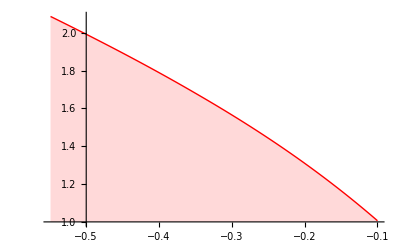

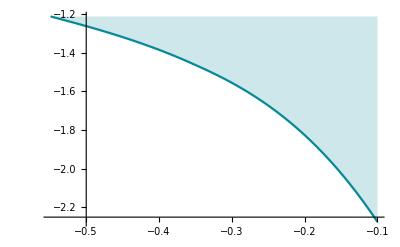

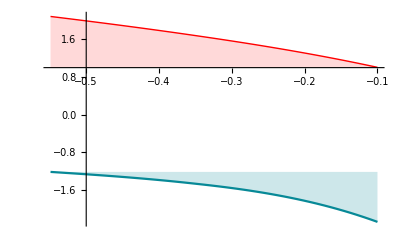

```mathematica
stabmatrixVaryk4=Table[({{k1, k2, k3}, {kval, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk4,{kval,k4Values}];
varyeigenk4=Table[Eigenvectors[stabmatrixVaryk4⟦index⟧],{index,1,Length[k4Values],1}];


varyeigenrealcompk4=Table[Table[Eigenvectors[stabmatrixVaryk4⟦index⟧],{index,1,Length[k4Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk4]}];

Subscript[v, ARR1k4]=Table[Table[Table[Eigenvectors[stabmatrixVaryk4⟦index⟧],{index,1,Length[k4Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk4]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk4]}];
Subscript[v, PLTk4]=Table[Table[Table[Eigenvectors[stabmatrixVaryk4⟦index⟧],{index,1,Length[k4Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk4]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk4]}];
Subscript[v, auxk4]=Table[Table[Table[Eigenvectors[stabmatrixVaryk4⟦index⟧],{index,1,Length[k4Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk4]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk4]}];


datak4 =Table[{k4Values⟦i⟧,Subscript[v, PLTk4]⟦i⟧/Subscript[v, auxk4]⟦i⟧},{i,1,Length[k4Values]}];
data2k4 =Table[{k4Values⟦i⟧,Subscript[v, ARR1k4]⟦i⟧/Subscript[v, PLTk4]⟦i⟧},{i,1,Length[k4Values]}];

interpolk4=Interpolation[datak4];
interpol2k4=Interpolation[data2k4];


plot1k4=Plot[interpolk4[x], {x,-0.549,-0.1},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k4=Plot[interpol2k4[x], {x,-0.549,-0.1},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k4,plot2k4]
```

```mathematica
k5Values=Table[n,{n,-6,3,0.1}];
```

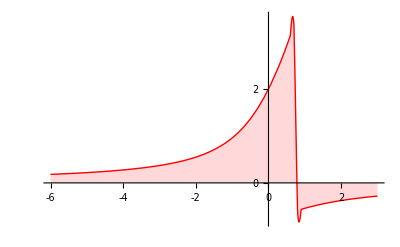

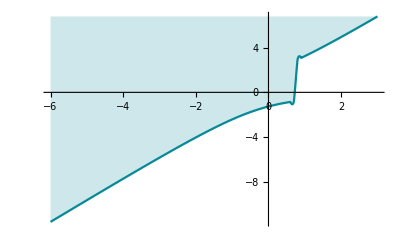

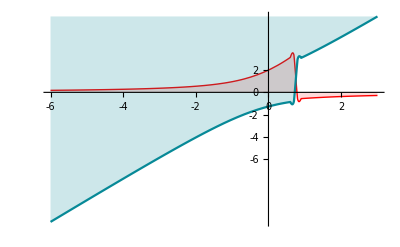

```mathematica
stabmatrixVaryk5=Table[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+kval, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk5,{kval,k5Values}];
varyeigenk5=Table[Eigenvectors[stabmatrixVaryk5⟦index⟧],{index,1,Length[k5Values],1}];


varyeigenrealcompk5=Table[Table[Eigenvectors[stabmatrixVaryk5⟦index⟧],{index,1,Length[k5Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk5]}];

Subscript[v, ARR1k5]=Table[Table[Table[Eigenvectors[stabmatrixVaryk5⟦index⟧],{index,1,Length[k5Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk5]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk5]}];
Subscript[v, PLTk5]=Table[Table[Table[Eigenvectors[stabmatrixVaryk5⟦index⟧],{index,1,Length[k5Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk5]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk5]}];
Subscript[v, auxk5]=Table[Table[Table[Eigenvectors[stabmatrixVaryk5⟦index⟧],{index,1,Length[k5Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk5]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk5]}];


datak5 =Table[{k5Values⟦i⟧,Subscript[v, PLTk5]⟦i⟧/Subscript[v, auxk5]⟦i⟧},{i,1,Length[k5Values]}];
data2k5 =Table[{k5Values⟦i⟧,Subscript[v, ARR1k5]⟦i⟧/Subscript[v, PLTk5]⟦i⟧},{i,1,Length[k5Values]}];

interpolk5=Interpolation[datak5];
interpol2k5=Interpolation[data2k5];

plot1k5=Plot[interpolk5[x], {x,-6,3},PlotRange->All,Ticks-> {{-6,-5.5,-5,-4.5,-4,-3.5,-3,-2.5,-2,-1.5,-1,-0.5,0,0.5,1,1.5,2,2.5,3}}, PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k5=Plot[interpol2k5[x], {x,-6,3},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k5,plot2k5]
```

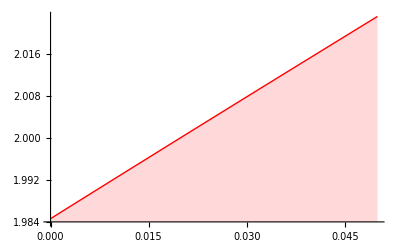

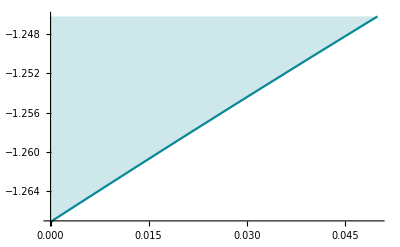

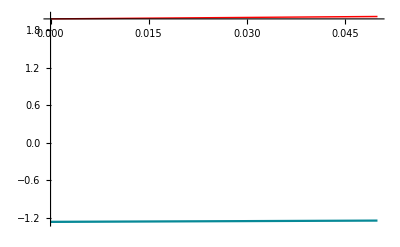

```mathematica
k6Values=Table[n,{n,0,0.05,0.01}];
stabmatrixVaryk6=Table[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, kval}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk6,{kval,k6Values}];
varyeigenk6=Table[Eigenvectors[stabmatrixVaryk6⟦index⟧],{index,1,Length[k6Values],1}];


varyeigenrealcompk6=Table[Table[Eigenvectors[stabmatrixVaryk6⟦index⟧],{index,1,Length[k6Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk6]}];

Subscript[v, ARR1k6]=Table[Table[Table[Eigenvectors[stabmatrixVaryk6⟦index⟧],{index,1,Length[k6Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk6]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk6]}];
Subscript[v, PLTk6]=Table[Table[Table[Eigenvectors[stabmatrixVaryk6⟦index⟧],{index,1,Length[k6Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk6]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk6]}];
Subscript[v, auxk6]=Table[Table[Table[Eigenvectors[stabmatrixVaryk6⟦index⟧],{index,1,Length[k6Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk6]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk6]}];


datak6 =Table[{k6Values⟦i⟧,Subscript[v, PLTk6]⟦i⟧/Subscript[v, auxk6]⟦i⟧},{i,1,Length[k6Values]}];
data2k6 =Table[{k6Values⟦i⟧,Subscript[v, ARR1k6]⟦i⟧/Subscript[v, PLTk6]⟦i⟧},{i,1,Length[k6Values]}];

interpolk6=Interpolation[datak6];
interpol2k6=Interpolation[data2k6];


plot1k6=Plot[interpolk6[x], {x,0,0.05},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k6=Plot[interpol2k6[x], {x,0,0.05},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k6,plot2k6]
```

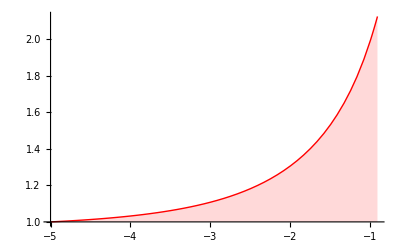

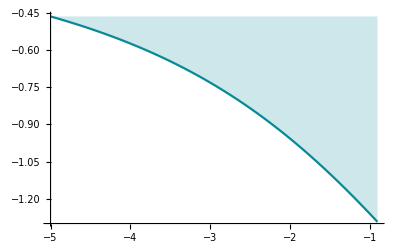

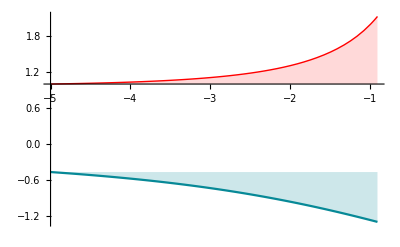

```mathematica
k7Values=Table[n,{n,-5,-0.911,0.1}];
stabmatrixVaryk7=Table[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {kval, k8, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk7,{kval,k7Values}];
varyeigenk7=Table[Eigenvectors[stabmatrixVaryk7⟦index⟧],{index,1,Length[k7Values],1}];


varyeigenrealcompk7=Table[Table[Eigenvectors[stabmatrixVaryk7⟦index⟧],{index,1,Length[k7Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk7]}];

Subscript[v, ARR1k7]=Table[Table[Table[Eigenvectors[stabmatrixVaryk7⟦index⟧],{index,1,Length[k7Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk7]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk7]}];
Subscript[v, PLTk7]=Table[Table[Table[Eigenvectors[stabmatrixVaryk7⟦index⟧],{index,1,Length[k7Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk7]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk7]}];
Subscript[v, auxk7]=Table[Table[Table[Eigenvectors[stabmatrixVaryk7⟦index⟧],{index,1,Length[k7Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk7]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk7]}];


datak7 =Table[{k7Values⟦i⟧,Subscript[v, PLTk7]⟦i⟧/Subscript[v, auxk7]⟦i⟧},{i,1,Length[k7Values]}];
data2k7 =Table[{k7Values⟦i⟧,Subscript[v, ARR1k7]⟦i⟧/Subscript[v, PLTk7]⟦i⟧},{i,1,Length[k7Values]}];

interpolk7=Interpolation[datak7];
interpol2k7=Interpolation[data2k7];


plot1k7=Plot[interpolk7[x], {x,-5,-0.911},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k7=Plot[interpol2k7[x], {x,-5,-0.911},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k7,plot2k7]
```

```mathematica
k8Values=Table[n,{n,0.12,0.219,0.01}];
```

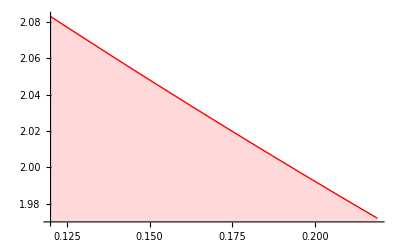

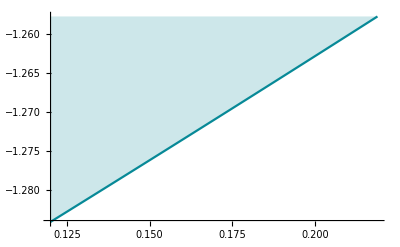

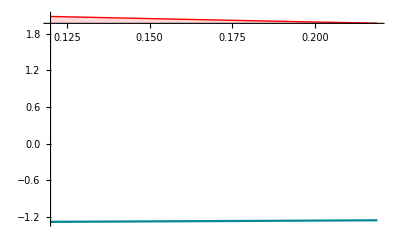

```mathematica
stabmatrixVaryk8=Table[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, kval, - Subscript[D, aux] (Subscript[k, max])^2+k9}})/.T1paramsvaryk8,{kval,k8Values}];
varyeigenk8=Table[Eigenvectors[stabmatrixVaryk8⟦index⟧],{index,1,Length[k8Values],1}];


varyeigenrealcompk8=Table[Table[Eigenvectors[stabmatrixVaryk8⟦index⟧],{index,1,Length[k8Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk8]}];

Subscript[v, ARR1k8]=Table[Table[Table[Eigenvectors[stabmatrixVaryk8⟦index⟧],{index,1,Length[k8Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk8]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk8]}];
Subscript[v, PLTk8]=Table[Table[Table[Eigenvectors[stabmatrixVaryk8⟦index⟧],{index,1,Length[k8Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk8]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk8]}];
Subscript[v, auxk8]=Table[Table[Table[Eigenvectors[stabmatrixVaryk8⟦index⟧],{index,1,Length[k8Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk8]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk8]}];


datak8 =Table[{k8Values⟦i⟧,Subscript[v, PLTk8]⟦i⟧/Subscript[v, auxk8]⟦i⟧},{i,1,Length[k8Values]}];
data2k8 =Table[{k8Values⟦i⟧,Subscript[v, ARR1k8]⟦i⟧/Subscript[v, PLTk8]⟦i⟧},{i,1,Length[k8Values]}];

interpolk8=Interpolation[datak8];
interpol2k8=Interpolation[data2k8];


plot1k8=Plot[interpolk8[x], {x,0.12,0.219},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k8=Plot[interpol2k8[x],{x,0.12,0.219},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k8,plot2k8]
```

```mathematica
k9Values=Table[n,{n,-0.18,-0.09,0.01}];
```

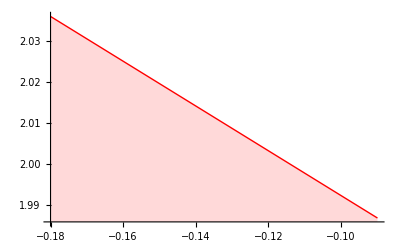

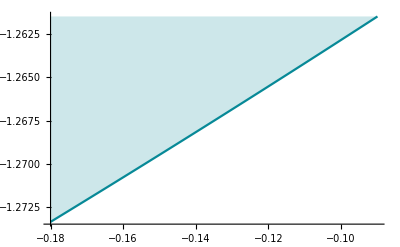

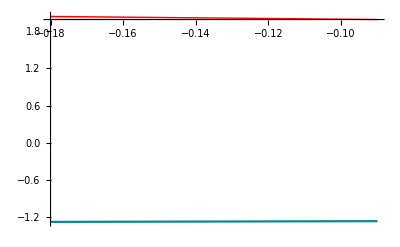

```mathematica
stabmatrixVaryk9=Table[({{k1, k2, k3}, {k4, -Subscript[D, PLT](Subscript[k, max])^2+k5, k6}, {k7, k8, - Subscript[D, aux] (Subscript[k, max])^2+kval}})/.T1paramsvaryk9,{kval,k9Values}];
varyeigenk9=Table[Eigenvectors[stabmatrixVaryk9⟦index⟧],{index,1,Length[k9Values],1}];


varyeigenrealcompk9=Table[Table[Eigenvectors[stabmatrixVaryk9⟦index⟧],{index,1,Length[k9Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk9]}];

Subscript[v, ARR1k9]=Table[Table[Table[Eigenvectors[stabmatrixVaryk9⟦index⟧],{index,1,Length[k9Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk9]}]⟦i⟧⟦1⟧,{i,1,Length[varyeigenk9]}];
Subscript[v, PLTk9]=Table[Table[Table[Eigenvectors[stabmatrixVaryk9⟦index⟧],{index,1,Length[k9Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk9]}]⟦i⟧⟦2⟧,{i,1,Length[varyeigenk9]}];
Subscript[v, auxk9]=Table[Table[Table[Eigenvectors[stabmatrixVaryk9⟦index⟧],{index,1,Length[k9Values],1}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk9]}]⟦i⟧⟦3⟧,{i,1,Length[varyeigenk9]}];


datak9 =Table[{k9Values⟦i⟧,Subscript[v, PLTk9]⟦i⟧/Subscript[v, auxk9]⟦i⟧},{i,1,Length[k9Values]}];
data2k9 =Table[{k9Values⟦i⟧,Subscript[v, ARR1k9]⟦i⟧/Subscript[v, PLTk9]⟦i⟧},{i,1,Length[k9Values]}];

interpolk9=Interpolation[datak9];
interpol2k9=Interpolation[data2k9];


plot1k9=Plot[interpolk9[x], {x,-0.18,-0.09},PlotRange->All,PlotStyle->{Directive[Red,Thin],Red},Filling-> Axis, FillingStyle->LightRed]
plot2k9=Plot[interpol2k9[x],{x,-0.18,-0.09},PlotRange->All,Filling->Top, FillingStyle->Automatic]
Show[plot1k9,plot2k9]
```

```mathematica
Plotting pdes to see in- or out- of phase components. I have substituted a saturation term for ARR1 as in Raspopovic
```

-or out+in pdes Plotting see to-a ARR1 as for have in of phase Raspopovic saturation substituted term components.ⅈ

```mathematica
Subscript[P, PIN][x,t]:=Piecewise[{{2,0≤x≤200}},0]
```

```mathematica
tFinal= 10000;
```

```mathematica
length=500;
lengthy=20;
arr1={D[ARR1[x,t],t]==k1 *ARR1[x,t]+ k2 *PLT[x,t]+k3*aux[x,t] +alpha-(ARR1[x,t])^3+Subscript[D, ARR1]*D[ARR1[x,t],x,x]};
plethora={D[PLT[x,t],t]==k4  *ARR1[x,t]+k5 *PLT[x,t]+k6 * aux[x,t]+ beta+Subscript[D, PLT]*D[PLT[x,t],x,x]};
(*testing polar transport everywhere (auxinAdvUnifTransp)or only in the MZ (first peak - auxinAdvTranspOnlyMZ)*)
auxinAdvUnifTransp={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]+Subscript[P, PIN]*D[aux[x,t],x]};
auxinAdvTranspOnlyMZ={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]+Subscript[P, PIN][x,t]*D[aux[x,t],x]};
(*without auxin polar transport, only diffusion)*)
auxinDiff={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]};

ic = {ARR1[x,t]==-0.1/.t->0,PLT[x,t]==-0.1/.t->0,aux[x,t]==-0.1/.t->0};
bcAdv= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0a/.x->length/.j0a -> 10^-3,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->length,ARR1[0,t]==-0.1, ARR1[length,t]==-0.1};
bcDiff= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==0/.x->length/.j0a -> 10^-3,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->length,ARR1[0,t]==0, ARR1[length,t]==0};

(*building the set of pdes for each case*)
pdesDiff = {plethora,arr1,auxinDiff};
pdesAdvUnif = {plethora,arr1,auxinAdvUnifTransp};
pdesAdvOnlyMZ = {plethora,arr1,auxinAdvTranspOnlyMZ};
```

```mathematica
D[aux[x,t],x]/.t-> 0/.x-> 0
```

aux^(1,0)[0,0]

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{ARR1→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>],PLT→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>],aux→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>]}}

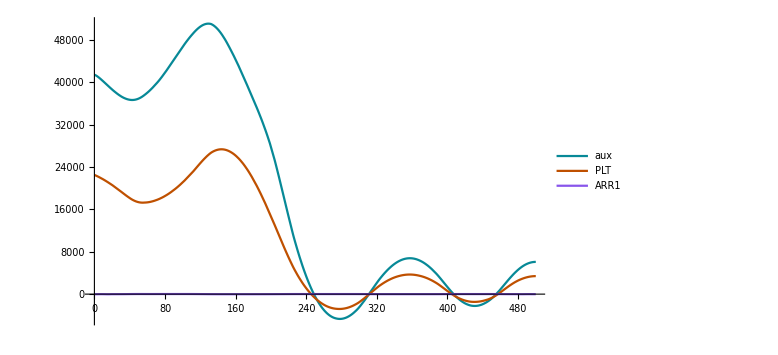

Method

```mathematica
solveAdv=NDSolve[{pdesAdvOnlyMZ,ic,bcAdv}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","DifferenceOrder"-> Pseudospectral}},PrecisionGoal->2]
solveplot= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveAdv[[1]]/.t->tFinal],{x,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
```

```mathematica
(*Manipulate[Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solve[[1]]],{x,0,length},PlotRange->All],{t,0,tFinal}]*)
```

```mathematica
k8/.ourParams
```

0.2

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{ARR1→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>],PLT→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>],aux→InterpolatingFunction[{{0., 500.}, {0., 10000.}}, <>]}}

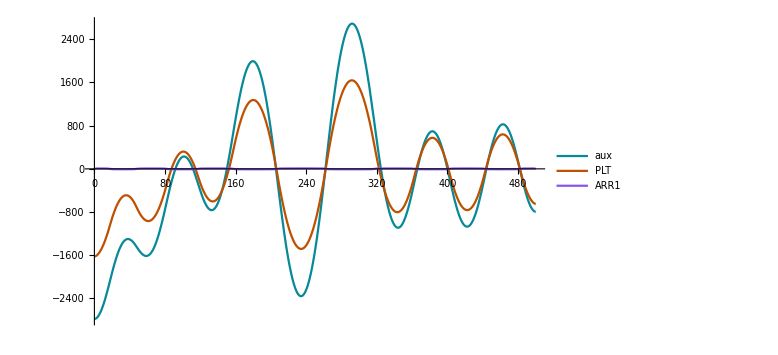

```mathematica
solveDiff=NDSolve[{pdesDiff,ic,bcDiff}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100}} ,PrecisionGoal->1]
solveplotDiff= Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solveDiff[[1]]/.t->tFinal],{x,0,length},PlotRange->All,PlotLegends->{aux,PLT,ARR1},ImageSize->Large]
```